```mathematica
DataFull = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_Empirical_Watersheds/Optimal_Channel_Nets/Results/dir_text/dir_m0_Full_S.csv","Data"];
LPFull =ListPlot3D[DataFull,Mesh->None,InterpolationOrder->3,ColorFunction->"DarkRainbow", PlotStyle->Directive[Opacity[0.75]],PlotRange->{0,0.5},AxesLabel->{"e/c","Prob(Directed)","Proportion"},ImageSize->400];
DataLattice = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_Empirical_Watersheds/Optimal_Channel_Nets/Results/dir_text/dir_m0_Lattice_S.csv","Data"];
LPLattice=ListPlot3D[DataLattice,Mesh->None,InterpolationOrder->3,ColorFunction->"DarkRainbow", PlotStyle->Directive[Opacity[0.75]],PlotRange->{0,0.5},AxesLabel->{"e/c","Prob(Directed)","Proportion"},ImageSize->400];
DataSF = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_Empirical_Watersheds/Optimal_Channel_Nets/Results/dir_text/dir_m0_SF_S.csv","Data"];
LPSF = ListPlot3D[DataSF,Mesh->None,InterpolationOrder->3,ColorFunction->"DarkRainbow", PlotStyle->Directive[Opacity[0.75]],PlotRange->{0,0.5},AxesLabel->{"e/c","Prob(Directed)","Proportion"},ImageSize->400];
GraphicsGrid[{{LPFull,LPLattice,LPSF}},ImageSize->800,Spacings->{0,0}]
```

-Graphics-

```mathematica
DataFull = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_Empirical_Watersheds/Optimal_Channel_Nets/Results/dir_text/dir_m0_Full_L.csv","Data"];
LPFull =ListPlot3D[DataFull,Mesh->None,InterpolationOrder->3,ColorFunction->"DarkRainbow", PlotStyle->Directive[Opacity[0.75]],PlotRange->{0,1},AxesLabel->{"e/c","Prob(Directed)","Proportion"},ImageSize->400];
DataLattice = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_Empirical_Watersheds/Optimal_Channel_Nets/Results/dir_text/dir_m0_Lattice_L.csv","Data"];
LPLattice=ListPlot3D[DataLattice,Mesh->None,InterpolationOrder->3,ColorFunction->"DarkRainbow", PlotStyle->Directive[Opacity[0.75]],PlotRange->{0,1},AxesLabel->{"e/c","Prob(Directed)","Proportion"},ImageSize->400];
DataSF = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_Empirical_Watersheds/Optimal_Channel_Nets/Results/dir_text/dir_m0_SF_L.csv","Data"];
LPSF = ListPlot3D[DataSF,Mesh->None,InterpolationOrder->3,ColorFunction->"DarkRainbow", PlotStyle->Directive[Opacity[0.75]],PlotRange->{0,1},AxesLabel->{"e/c","Prob(Directed)","Proportion"},ImageSize->400];
GraphicsGrid[{{LPFull,LPLattice,LPSF}},ImageSize->1200,Spacings->{0,0}]
```

-Graphics-

```mathematica
DataFullS = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_Empirical_Watersheds/Optimal_Channel_Nets/Results/dir_text/dir_m0_Full_S.csv","Data"];
DataFullL = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_Empirical_Watersheds/Optimal_Channel_Nets/Results/dir_text/dir_m0_Full_L.csv","Data"];
DataFull = DataFullS + DataFullL;
LPFull =ListPlot3D[DataFull,Mesh->None,InterpolationOrder->3,ColorFunction->"DarkRainbow", PlotStyle->Directive[Opacity[0.75]],PlotRange->{0,1},AxesLabel->{"e/c","Prob(Directed)","Proportion"},ImageSize->400];
DataLatticeS = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_Empirical_Watersheds/Optimal_Channel_Nets/Results/dir_text/dir_m0_Lattice_S.csv","Data"];
DataLatticeL = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_Empirical_Watersheds/Optimal_Channel_Nets/Results/dir_text/dir_m0_Lattice_L.csv","Data"];
DataLattice = DataLatticeS + DataLatticeL;
LPLattice=ListPlot3D[DataLattice,Mesh->None,InterpolationOrder->3,ColorFunction->"DarkRainbow", PlotStyle->Directive[Opacity[0.75]],PlotRange->{0,1},AxesLabel->{"e/c","Prob(Directed)","Proportion"},ImageSize->400];
DataSFS = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_Empirical_Watersheds/Optimal_Channel_Nets/Results/dir_text/dir_m0_SF_S.csv","Data"];
DataSFL = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_Empirical_Watersheds/Optimal_Channel_Nets/Results/dir_text/dir_m0_SF_L.csv","Data"];
DataSF = DataSFS + DataSFL;
LPSF = ListPlot3D[DataSF,Mesh->None,InterpolationOrder->3,ColorFunction->"DarkRainbow", PlotStyle->Directive[Opacity[0.75]],PlotRange->{0,1},AxesLabel->{"e/c","Prob(Directed)","Proportion"},ImageSize->400];
GraphicsGrid[{{LPFull,LPLattice,LPSF}},ImageSize->1200,Spacings->{0,0}]
```

-Graphics-

```mathematica
DataSFS = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_Empirical_Watersheds/Optimal_Channel_Nets/Results/dir_text/dir_m0_SF_S.csv","Data"];
DataSFL = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_Empirical_Watersheds/Optimal_Channel_Nets/Results/dir_text/dir_m0_SF_L.csv","Data"];
```

```mathematica
DataSFS + DataSFL
```

{{0,0,1},{0.2,0,0.988934},{0.4,0,0.955382},{0.6,0,0.90339},{0.8,0,0.837178},{1.,0,0.767258},{1.2,0,0.689902},{1.4,0,0.62211},{1.6,0,0.555122},{1.8,0,0.49376},{2,0,0.43932},{2.2,0,0.386653},{2.4,0,0.337206},{2.6,0,0.172101},{2.8,0,0},{3.,0,0},{3.2,0,0},{3.4,0,0},{3.6,0,0},{3.8,0,0},{4,0,0},{0,0.2,1},{0.2,0.2,0.988983},{0.4,0.2,0.954563},{0.6,0.2,0.902229},{0.8,0.2,0.836979},{1.,0.2,0.762139},{1.2,0.2,0.688811},{1.4,0.2,0.616739},{1.6,0.2,0.54978},{1.8,0.2,0.497909},{2,0.2,0.436203},{2.2,0.2,0.346319},{2.4,0.2,0.333452},{2.6,0.2,0.113458},{2.8,0.2,0},{3.,0.2,0},{3.2,0.2,0},{3.4,0.2,0},{3.6,0.2,0},{3.8,0.2,0},{4,0.2,0},{0,0.4,0.99},{0.2,0.4,0.969043},{0.4,0.4,0.935652},{0.6,0.4,0.88363},{0.8,0.4,0.818611},{1.,0.4,0.748417},{1.2,0.4,0.672867},{1.4,0.4,0.6057},{1.6,0.4,0.538852},{1.8,0.4,0.47728},{2,0.4,0.42315},{2.2,0.4,0.37002},{2.4,0.4,0.242625},{2.6,0.4,0.047944},{2.8,0.4,0.0222312},{3.,0.4,0},{3.2,0.4,0},{3.4,0.4,0},{3.6,0.4,0},{3.8,0.4,0},{4,0.4,0},{0,0.6,0.97},{0.2,0.6,0.941344},{0.4,0.6,0.897148},{0.6,0.6,0.845867},{0.8,0.6,0.785512},{1.,0.6,0.713415},{1.2,0.6,0.646392},{1.4,0.6,0.576721},{1.6,0.6,0.515789},{1.8,0.6,0.456102},{2,0.6,0.404595},{2.2,0.6,0.349809},{2.4,0.6,0.271711},{2.6,0.6,0.0304484},{2.8,0.6,0},{3.,0.6,0},{3.2,0.6,0},{3.4,0.6,0},{3.6,0.6,0},{3.8,0.6,0},{4,0.6,0},{0,0.8,0.98},{0.2,0.8,0.890084},{0.4,0.8,0.859396},{0.6,0.8,0.810476},{0.8,0.8,0.750394},{1.,0.8,0.684271},{1.2,0.8,0.615205},{1.4,0.8,0.545235},{1.6,0.8,0.483521},{1.8,0.8,0.427266},{2,0.8,0.366623},{2.2,0.8,0.302142},{2.4,0.8,0.11619},{2.6,0.8,0.0176144},{2.8,0.8,0},{3.,0.8,0},{3.2,0.8,0},{3.4,0.8,0},{3.6,0.8,0},{3.8,0.8,0},{4,0.8,0},{0,1.,0.94},{0.2,1.,0.859857},{0.4,1.,0.829185},{0.6,1.,0.780296},{0.8,1.,0.720991},{1.,1.,0.652588},{1.2,1.,0.585482},{1.4,1.,0.519081},{1.6,1.,0.454034},{1.8,1.,0.401789},{2,1.,0.311731},{2.2,1.,0.147029},{2.4,1.,0.0256048},{2.6,1.,0},{2.8,1.,0},{3.,1.,0},{3.2,1.,0},{3.4,1.,0},{3.6,1.,0},{3.8,1.,0},{4,1.,0},{0,1.2,0.92},{0.2,1.2,0.843901},{0.4,1.2,0.800604},{0.6,1.2,0.755129},{0.8,1.2,0.696698},{1.,1.2,0.632679},{1.2,1.2,0.570947},{1.4,1.2,0.5036},{1.6,1.2,0.441976},{1.8,1.2,0.380663},{2,1.2,0.325198},{2.2,1.2,0.131169},{2.4,1.2,0.0126052},{2.6,1.2,0},{2.8,1.2,0},{3.,1.2,0},{3.2,1.2,0},{3.4,1.2,0},{3.6,1.2,0},{3.8,1.2,0},{4,1.2,0},{0,1.4,0.93},{0.2,1.4,0.771},{0.4,1.4,0.74385},{0.6,1.4,0.701308},{0.8,1.4,0.648096},{1.,1.4,0.587026},{1.2,1.4,0.523572},{1.4,1.4,0.462695},{1.6,1.4,0.405025},{1.8,1.4,0.3361},{2,1.4,0.165184},{2.2,1.4,0.0015684},{2.4,1.4,0},{2.6,1.4,0},{2.8,1.4,0},{3.,1.4,0},{3.2,1.4,0},{3.4,1.4,0},{3.6,1.4,0},{3.8,1.4,0},{4,1.4,0},{0,1.6,0.9},{0.2,1.6,0.770257},{0.4,1.6,0.741215},{0.6,1.6,0.694052},{0.8,1.6,0.636353},{1.,1.6,0.569432},{1.2,1.6,0.50076},{1.4,1.6,0.437882},{1.6,1.6,0.344252},{1.8,1.6,0.248957},{2,1.6,0.0341324},{2.2,1.6,0},{2.4,1.6,0},{2.6,1.6,0},{2.8,1.6,0},{3.,1.6,0},{3.2,1.6,0},{3.4,1.6,0},{3.6,1.6,0},{3.8,1.6,0},{4,1.6,0},{0,1.8,0.88},{0.2,1.8,0.711295},{0.4,1.8,0.684386},{0.6,1.8,0.643682},{0.8,1.8,0.59321},{1.,1.8,0.536491},{1.2,1.8,0.479704},{1.4,1.8,0.418924},{1.6,1.8,0.361158},{1.8,1.8,0.25634},{2,1.8,0.048394},{2.2,1.8,0.0034824},{2.4,1.8,0},{2.6,1.8,0},{2.8,1.8,0},{3.,1.8,0},{3.2,1.8,0},{3.4,1.8,0},{3.6,1.8,0},{3.8,1.8,0},{4,1.8,0},{0,2,0.91},{0.2,2,0.671642},{0.4,2,0.645977},{0.6,2,0.603034},{0.8,2,0.549272},{1.,2,0.484411},{1.2,2,0.420005},{1.4,2,0.317542},{1.6,2,0.123792},{1.8,2,0},{2,2,0},{2.2,2,0},{2.4,2,0},{2.6,2,0},{2.8,2,0},{3.,2,0},{3.2,2,0},{3.4,2,0},{3.6,2,0},{3.8,2,0},{4,2,0}}

```mathematica
DataFull2 =DataFull;
DataFull2[[All,2]] = DataFull[[All,3]];
DataFull2[[All,3]] = DataFull[[All,2]];

DataLattice2 =DataLattice;
DataLattice2[[All,2]] = DataLattice[[All,3]];
DataLattice2[[All,3]] = DataLattice[[All,2]];

DataSF2 =DataSF;
DataSF2[[All,2]] = DataSF[[All,3]];
DataSF2[[All,3]] = DataSF[[All,2]];
```

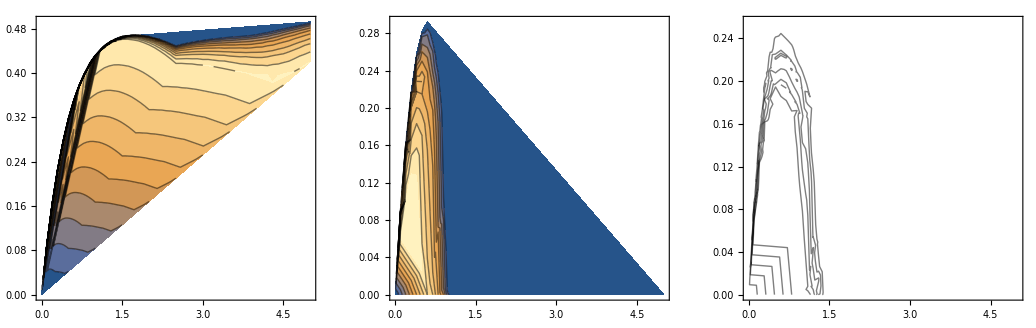

```mathematica
GraphicsGrid[{{ListContourPlot[DataFull2],ListContourPlot[DataLattice2],ListContourPlot[DataSF2,ContourShading->None,Contours->5]}}]
```

```mathematica
DataFull[[All,2]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
L=Table[0,{10}];
Table[
L[[i+1]]=Take[DataFull[[All,3]],Flatten[{First[Position[DataFull[[All,2]],N[i/10]]],Last[Position[DataFull[[All,2]],N[i/10]]]}]],
{i,0,10,1}];
```

First::nofirst: {} has a length of zero and no first element.

Last::nolast: {} has a length of zero and no last element.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{0, 0.0904672, 0.164459, 0.225421, 0.275781, 0.316593, 0.348973, 0.377428, 0.398424, 0.416702, 0.431312, 0.442464, 0.451235, 0.456972, 0.463095, 0.465931, 0.46786, 0.468348, 0.468355, 0.467839, 0.465801, 0.463675, 0.460795, 0.45793, 0.454168, 0.450222, 0.452651, 0.455044, 0.456964, 0.458876, 0.46026, 0.462035, 0.463226, 0.4645, 0.465338, 0.466302, 0.467359, 0.468147, 0.469053, 0.470139, 0.471471, 0.473673, 0.475346, 0.47744, 0.479311, 0.481457, 0.483793, 0.485737, 0.487903, 0.490347, « 511 »}, {First[{}], Last[{}]}].

First::nofirst: {} has a length of zero and no first element.

Last::nolast: {} has a length of zero and no last element.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{0, 0.0904672, 0.164459, 0.225421, 0.275781, 0.316593, 0.348973, 0.377428, 0.398424, 0.416702, 0.431312, 0.442464, 0.451235, 0.456972, 0.463095, 0.465931, 0.46786, 0.468348, 0.468355, 0.467839, 0.465801, 0.463675, 0.460795, 0.45793, 0.454168, 0.450222, 0.452651, 0.455044, 0.456964, 0.458876, 0.46026, 0.462035, 0.463226, 0.4645, 0.465338, 0.466302, 0.467359, 0.468147, 0.469053, 0.470139, 0.471471, 0.473673, 0.475346, 0.47744, 0.479311, 0.481457, 0.483793, 0.485737, 0.487903, 0.490347, « 511 »}, {First[{}], Last[{}]}].

Set::partw: Part 11 of {Take[{0, 0.0904672, 0.164459, 0.225421, 0.275781, 0.316593, 0.348973, 0.377428, 0.398424, 0.416702, 0.431312, 0.442464, 0.451235, 0.456972, 0.463095, 0.465931, 0.46786, 0.468348, 0.468355, 0.467839, 0.465801, 0.463675, 0.460795, 0.45793, 0.454168, 0.450222, 0.452651, 0.455044, 0.456964, 0.458876, 0.46026, 0.462035, 0.463226, 0.4645, 0.465338, 0.466302, 0.467359, 0.468147, 0.469053, 0.470139, 0.471471, 0.473673, 0.475346, 0.47744, 0.479311, 0.481457, 0.483793, 0.485737, 0.487903, 0.490347, « 511 »}, {First[{}], Last[{}]}], {« 1 »}, « 7 », {0, « 49 », « 1 »}} does not exist.

```mathematica
L = Delete[L[[11]]]
```

Part::partw: Part 11 of {Take[{0, 0.0904672, 0.164459, 0.225421, 0.275781, 0.316593, 0.348973, 0.377428, 0.398424, 0.416702, 0.431312, 0.442464, 0.451235, 0.456972, 0.463095, 0.465931, 0.46786, 0.468348, 0.468355, 0.467839, 0.465801, 0.463675, 0.460795, 0.45793, 0.454168, 0.450222, 0.452651, 0.455044, 0.456964, 0.458876, 0.46026, 0.462035, 0.463226, 0.4645, 0.465338, 0.466302, 0.467359, 0.468147, 0.469053, 0.470139, 0.471471, 0.473673, 0.475346, 0.47744, 0.479311, 0.481457, 0.483793, 0.485737, 0.487903, 0.490347, « 511 »}, {First[{}], Last[{}]}], « 8 », {0, « 49 », « 1 »}} ⟦ -11 ⟧ does not exist.

Delete[{Take[{0,0.0904672,0.164459,0.225421,0.275781,0.316593,0.348973,0.377428,0.398424,0.416702,0.431312,0.442464,0.451235,0.456972,0.463095,0.465931,0.46786,0.468348,0.468355,0.467839,0.465801,0.463675,0.460795,0.45793,0.454168,0.450222,0.452651,0.455044,0.456964,0.458876,0.46026,0.462035,0.463226,0.4645,0.465338,0.466302,0.467359,0.468147,0.469053,0.470139,0.471471,0.473673,0.475346,0.47744,0.479311,0.481457,0.483793,0.485737,0.487903,0.490347,0.492448,0,0.0904988,0.164887,0.225508,0.276839,0.316946,0.351196,0.376283,0.399053,0.415762,0.43181,0.441779,0.450636,0.457791,0.462161,0.465679,0.467573,0.468749,0.467957,0.467762,0.466141,0.463149,0.460864,0.457052,0.453159,0.449117,0.451655,0.453835,0.45562,0.457405,0.458817,0.460375,0.461478,0.462588,0.463647,0.464592,0.465329,0.465975,0.46673,0.467774,0.469095,0.471262,0.472761,0.475166,0.477301,0.479581,0.481598,0.483909,0.48613,0.48823,0.490457,0,0.0906808,0.165444,0.225957,0.276114,0.316766,0.34958,0.377083,0.398901,0.417709,0.430318,0.44302,0.450853,0.457511,0.462207,0.465314,0.467181,0.468692,0.468296,0.467016,0.465737,0.462728,0.459905,0.456618,0.452234,0.447909,0.450308,0.452395,0.45416,0.455761,0.456996,0.458439,0.459532,0.460305,0.461246,0.462065,0.462526,0.463222,0.464053,0.4649,0.466298,0.468495,0.470078,0.471975,0.47445,0.476748,0.47891,0.481242,0.483625,0.485847,0.488166,0,0.0900048,0.164366,0.225412,0.275663,0.316606,0.349659,0.376686,0.398676,0.417049,0.430977,0.44235,0.450096,0.458184,0.461745,0.465256,0.467462,0.468238,0.46777,0.466706,0.464813,0.46238,0.458925,0.455232,0.451118,0.446502,0.448601,0.450426,0.452204,0.453494,0.454809,0.455966,0.45672,0.457653,0.458338,0.458759,0.459505,0.460358,0.46099,0.461947,0.463106,0.464706,0.465983,0.468752,0.470742,0.473353,0.475901,0.478148,0.480466,0.48325,0.485446,0,0.090478,0.16608,0.226821,0.27524,0.315528,0.349746,0.37646,0.39843,0.415866,0.431662,0.442307,0.450706,0.457401,0.462146,0.46601,0.467227,0.467422,0.466887,0.465847,0.463902,0.46107,0.45779,0.453898,0.449404,0.444508,0.446589,0.448269,0.449719,0.450934,0.4519,0.452768,0.453456,0.454088,0.454426,0.455152,0.45536,0.455996,0.456518,0.457087,0.458537,0.45965,0.461187,0.463563,0.465985,0.468928,0.471467,0.474,0.476599,0.479014,0.48134,0,0.0917264,0.164202,0.226184,0.27537,0.316046,0.349831,0.376274,0.398699,0.417519,0.430994,0.441951,0.45051,0.457044,0.461593,0.464089,0.466491,0.467287,0.466349,0.465214,0.463069,0.459912,0.456675,0.452071,0.447576,0.442409,0.444113,0.445587,0.446993,0.447983,0.448692,0.449293,0.449793,0.45034,0.450626,0.450582,0.450685,0.451336,0.45132,0.451815,0.45317,0.45415,0.456656,0.457801,0.460406,0.463542,0.466164,0.46841,0.471612,0.474215,0.477096,0,0.089996,0.164534,0.225184,0.275108,0.316425,0.349921,0.377574,0.398381,0.416453,0.431386,0.441474,0.451511,0.457608,0.46179,0.464605,0.466451,0.465764,0.46561,0.463968,0.461352,0.458142,0.454372,0.450182,0.444956,0.439396,0.441048,0.441924,0.443244,0.444034,0.444562,0.444983,0.445082,0.445528,0.444892,0.445262,0.44526,0.445483,0.44498,0.44551,0.446689,0.446984,0.449212,0.450425,0.45325,0.455806,0.45824,0.461853,0.464783,0.467856,0.470736,0,0.0905724,0.164094,0.225201,0.275233,0.318009,0.350042,0.377082,0.398461,0.418092,0.430995,0.441409,0.450251,0.456961,0.461455,0.463414,0.46508,0.465581,0.464965,0.462338,0.459903,0.456527,0.452265,0.447233,0.441675,0.435536,0.43692,0.437566,0.438428,0.438876,0.438914,0.439211,0.439176,0.438966,0.438517,0.438275,0.437414,0.437413,0.436993,0.437315,0.437398,0.43776,0.438996,0.440543,0.443125,0.445324,0.448357,0.45216,0.455705,0.458752,0.462388,0,0.0906408,0.164822,0.226076,0.275217,0.316774,0.349794,0.378078,0.397896,0.415801,0.431251,0.441346,0.451048,0.456466,0.461368,0.463528,0.464525,0.464515,0.463245,0.460694,0.457949,0.454064,0.449308,0.443884,0.438286,0.431826,0.432671,0.433152,0.433556,0.433639,0.433846,0.433533,0.433032,0.432318,0.43205,0.430684,0.430029,0.42933,0.429639,0.428514,0.4281,0.428056,0.429288,0.431434,0.433132,0.434807,0.43819,0.442028,0.445795,0.450271,0.453024,0,0.0911892,0.164002,0.226442,0.275501,0.315642,0.350168,0.375639,0.398925,0.416808,0.430716,0.4419,0.449518,0.455918,0.459656,0.462116,0.462705,0.462543,0.461237,0.45831,0.454838,0.450442,0.44512,0.439289,0.432605,0.425514,0.425794,0.42609,0.42576,0.425829,0.424531,0.424574,0.423351,0.422134,0.421748,0.420015,0.418452,0.41662,0.415931,0.414787,0.41405,0.414086,0.413373,0.415459,0.416303,0.418976,0.4214,0.425854,0.430639,0.43414,0.438265,0,0.0905176,0.163764,0.226272,0.275115,0.315933,0.349676,0.37713,0.398953,0.415762,0.430503,0.440922,0.448662,0.454992,0.45878,0.460912,0.461094,0.459879,0.458217,0.454912,0.450913,0.445916,0.43983,0.433129,0.425672,0.417405,0.417524,0.41684,0.416474,0.415064,0.414415,0.413625,0.41174,0.409788,0.407904,0.405925,0.403838,0.402444,0.400313,0.398594,0.397082,0.39653,0.396548,0.383274,0.395566,0.398328,0.400614,0.40288,0.408103,0.414588,0.420413},{First[{}],Last[{}]}],{0,0.0904988,0.164887,0.225508,0.276839,0.316946,0.351196,0.376283,0.399053,0.415762,0.43181,0.441779,0.450636,0.457791,0.462161,0.465679,0.467573,0.468749,0.467957,0.467762,0.466141,0.463149,0.460864,0.457052,0.453159,0.449117,0.451655,0.453835,0.45562,0.457405,0.458817,0.460375,0.461478,0.462588,0.463647,0.464592,0.465329,0.465975,0.46673,0.467774,0.469095,0.471262,0.472761,0.475166,0.477301,0.479581,0.481598,0.483909,0.48613,0.48823,0.490457},{0,0.0906808,0.165444,0.225957,0.276114,0.316766,0.34958,0.377083,0.398901,0.417709,0.430318,0.44302,0.450853,0.457511,0.462207,0.465314,0.467181,0.468692,0.468296,0.467016,0.465737,0.462728,0.459905,0.456618,0.452234,0.447909,0.450308,0.452395,0.45416,0.455761,0.456996,0.458439,0.459532,0.460305,0.461246,0.462065,0.462526,0.463222,0.464053,0.4649,0.466298,0.468495,0.470078,0.471975,0.47445,0.476748,0.47891,0.481242,0.483625,0.485847,0.488166},{0,0.0900048,0.164366,0.225412,0.275663,0.316606,0.349659,0.376686,0.398676,0.417049,0.430977,0.44235,0.450096,0.458184,0.461745,0.465256,0.467462,0.468238,0.46777,0.466706,0.464813,0.46238,0.458925,0.455232,0.451118,0.446502,0.448601,0.450426,0.452204,0.453494,0.454809,0.455966,0.45672,0.457653,0.458338,0.458759,0.459505,0.460358,0.46099,0.461947,0.463106,0.464706,0.465983,0.468752,0.470742,0.473353,0.475901,0.478148,0.480466,0.48325,0.485446},{0,0.090478,0.16608,0.226821,0.27524,0.315528,0.349746,0.37646,0.39843,0.415866,0.431662,0.442307,0.450706,0.457401,0.462146,0.46601,0.467227,0.467422,0.466887,0.465847,0.463902,0.46107,0.45779,0.453898,0.449404,0.444508,0.446589,0.448269,0.449719,0.450934,0.4519,0.452768,0.453456,0.454088,0.454426,0.455152,0.45536,0.455996,0.456518,0.457087,0.458537,0.45965,0.461187,0.463563,0.465985,0.468928,0.471467,0.474,0.476599,0.479014,0.48134},{0,0.0917264,0.164202,0.226184,0.27537,0.316046,0.349831,0.376274,0.398699,0.417519,0.430994,0.441951,0.45051,0.457044,0.461593,0.464089,0.466491,0.467287,0.466349,0.465214,0.463069,0.459912,0.456675,0.452071,0.447576,0.442409,0.444113,0.445587,0.446993,0.447983,0.448692,0.449293,0.449793,0.45034,0.450626,0.450582,0.450685,0.451336,0.45132,0.451815,0.45317,0.45415,0.456656,0.457801,0.460406,0.463542,0.466164,0.46841,0.471612,0.474215,0.477096},{0,0.089996,0.164534,0.225184,0.275108,0.316425,0.349921,0.377574,0.398381,0.416453,0.431386,0.441474,0.451511,0.457608,0.46179,0.464605,0.466451,0.465764,0.46561,0.463968,0.461352,0.458142,0.454372,0.450182,0.444956,0.439396,0.441048,0.441924,0.443244,0.444034,0.444562,0.444983,0.445082,0.445528,0.444892,0.445262,0.44526,0.445483,0.44498,0.44551,0.446689,0.446984,0.449212,0.450425,0.45325,0.455806,0.45824,0.461853,0.464783,0.467856,0.470736},{0,0.0905724,0.164094,0.225201,0.275233,0.318009,0.350042,0.377082,0.398461,0.418092,0.430995,0.441409,0.450251,0.456961,0.461455,0.463414,0.46508,0.465581,0.464965,0.462338,0.459903,0.456527,0.452265,0.447233,0.441675,0.435536,0.43692,0.437566,0.438428,0.438876,0.438914,0.439211,0.439176,0.438966,0.438517,0.438275,0.437414,0.437413,0.436993,0.437315,0.437398,0.43776,0.438996,0.440543,0.443125,0.445324,0.448357,0.45216,0.455705,0.458752,0.462388},{0,0.0906408,0.164822,0.226076,0.275217,0.316774,0.349794,0.378078,0.397896,0.415801,0.431251,0.441346,0.451048,0.456466,0.461368,0.463528,0.464525,0.464515,0.463245,0.460694,0.457949,0.454064,0.449308,0.443884,0.438286,0.431826,0.432671,0.433152,0.433556,0.433639,0.433846,0.433533,0.433032,0.432318,0.43205,0.430684,0.430029,0.42933,0.429639,0.428514,0.4281,0.428056,0.429288,0.431434,0.433132,0.434807,0.43819,0.442028,0.445795,0.450271,0.453024},{0,0.0911892,0.164002,0.226442,0.275501,0.315642,0.350168,0.375639,0.398925,0.416808,0.430716,0.4419,0.449518,0.455918,0.459656,0.462116,0.462705,0.462543,0.461237,0.45831,0.454838,0.450442,0.44512,0.439289,0.432605,0.425514,0.425794,0.42609,0.42576,0.425829,0.424531,0.424574,0.423351,0.422134,0.421748,0.420015,0.418452,0.41662,0.415931,0.414787,0.41405,0.414086,0.413373,0.415459,0.416303,0.418976,0.4214,0.425854,0.430639,0.43414,0.438265}}⟦-11⟧⟦11⟧]

```mathematica
L[[11]]
```

Part::partw: Part 11 of {Take[{0, 0.0904672, 0.164459, 0.225421, 0.275781, 0.316593, 0.348973, 0.377428, 0.398424, 0.416702, 0.431312, 0.442464, 0.451235, 0.456972, 0.463095, 0.465931, 0.46786, 0.468348, 0.468355, 0.467839, 0.465801, 0.463675, 0.460795, 0.45793, 0.454168, 0.450222, 0.452651, 0.455044, 0.456964, 0.458876, 0.46026, 0.462035, 0.463226, 0.4645, 0.465338, 0.466302, 0.467359, 0.468147, 0.469053, 0.470139, 0.471471, 0.473673, 0.475346, 0.47744, 0.479311, 0.481457, 0.483793, 0.485737, 0.487903, 0.490347, « 511 »}, {First[{}], Last[{}]}], {« 1 »}, « 7 », {0, « 49 », « 1 »}} does not exist.

{Take[{0,0.0904672,0.164459,0.225421,0.275781,0.316593,0.348973,0.377428,0.398424,0.416702,0.431312,0.442464,0.451235,0.456972,0.463095,0.465931,0.46786,0.468348,0.468355,0.467839,0.465801,0.463675,0.460795,0.45793,0.454168,0.450222,0.452651,0.455044,0.456964,0.458876,0.46026,0.462035,0.463226,0.4645,0.465338,0.466302,0.467359,0.468147,0.469053,0.470139,0.471471,0.473673,0.475346,0.47744,0.479311,0.481457,0.483793,0.485737,0.487903,0.490347,0.492448,0,0.0904988,0.164887,0.225508,0.276839,0.316946,0.351196,0.376283,0.399053,0.415762,0.43181,0.441779,0.450636,0.457791,0.462161,0.465679,0.467573,0.468749,0.467957,0.467762,0.466141,0.463149,0.460864,0.457052,0.453159,0.449117,0.451655,0.453835,0.45562,0.457405,0.458817,0.460375,0.461478,0.462588,0.463647,0.464592,0.465329,0.465975,0.46673,0.467774,0.469095,0.471262,0.472761,0.475166,0.477301,0.479581,0.481598,0.483909,0.48613,0.48823,0.490457,0,0.0906808,0.165444,0.225957,0.276114,0.316766,0.34958,0.377083,0.398901,0.417709,0.430318,0.44302,0.450853,0.457511,0.462207,0.465314,0.467181,0.468692,0.468296,0.467016,0.465737,0.462728,0.459905,0.456618,0.452234,0.447909,0.450308,0.452395,0.45416,0.455761,0.456996,0.458439,0.459532,0.460305,0.461246,0.462065,0.462526,0.463222,0.464053,0.4649,0.466298,0.468495,0.470078,0.471975,0.47445,0.476748,0.47891,0.481242,0.483625,0.485847,0.488166,0,0.0900048,0.164366,0.225412,0.275663,0.316606,0.349659,0.376686,0.398676,0.417049,0.430977,0.44235,0.450096,0.458184,0.461745,0.465256,0.467462,0.468238,0.46777,0.466706,0.464813,0.46238,0.458925,0.455232,0.451118,0.446502,0.448601,0.450426,0.452204,0.453494,0.454809,0.455966,0.45672,0.457653,0.458338,0.458759,0.459505,0.460358,0.46099,0.461947,0.463106,0.464706,0.465983,0.468752,0.470742,0.473353,0.475901,0.478148,0.480466,0.48325,0.485446,0,0.090478,0.16608,0.226821,0.27524,0.315528,0.349746,0.37646,0.39843,0.415866,0.431662,0.442307,0.450706,0.457401,0.462146,0.46601,0.467227,0.467422,0.466887,0.465847,0.463902,0.46107,0.45779,0.453898,0.449404,0.444508,0.446589,0.448269,0.449719,0.450934,0.4519,0.452768,0.453456,0.454088,0.454426,0.455152,0.45536,0.455996,0.456518,0.457087,0.458537,0.45965,0.461187,0.463563,0.465985,0.468928,0.471467,0.474,0.476599,0.479014,0.48134,0,0.0917264,0.164202,0.226184,0.27537,0.316046,0.349831,0.376274,0.398699,0.417519,0.430994,0.441951,0.45051,0.457044,0.461593,0.464089,0.466491,0.467287,0.466349,0.465214,0.463069,0.459912,0.456675,0.452071,0.447576,0.442409,0.444113,0.445587,0.446993,0.447983,0.448692,0.449293,0.449793,0.45034,0.450626,0.450582,0.450685,0.451336,0.45132,0.451815,0.45317,0.45415,0.456656,0.457801,0.460406,0.463542,0.466164,0.46841,0.471612,0.474215,0.477096,0,0.089996,0.164534,0.225184,0.275108,0.316425,0.349921,0.377574,0.398381,0.416453,0.431386,0.441474,0.451511,0.457608,0.46179,0.464605,0.466451,0.465764,0.46561,0.463968,0.461352,0.458142,0.454372,0.450182,0.444956,0.439396,0.441048,0.441924,0.443244,0.444034,0.444562,0.444983,0.445082,0.445528,0.444892,0.445262,0.44526,0.445483,0.44498,0.44551,0.446689,0.446984,0.449212,0.450425,0.45325,0.455806,0.45824,0.461853,0.464783,0.467856,0.470736,0,0.0905724,0.164094,0.225201,0.275233,0.318009,0.350042,0.377082,0.398461,0.418092,0.430995,0.441409,0.450251,0.456961,0.461455,0.463414,0.46508,0.465581,0.464965,0.462338,0.459903,0.456527,0.452265,0.447233,0.441675,0.435536,0.43692,0.437566,0.438428,0.438876,0.438914,0.439211,0.439176,0.438966,0.438517,0.438275,0.437414,0.437413,0.436993,0.437315,0.437398,0.43776,0.438996,0.440543,0.443125,0.445324,0.448357,0.45216,0.455705,0.458752,0.462388,0,0.0906408,0.164822,0.226076,0.275217,0.316774,0.349794,0.378078,0.397896,0.415801,0.431251,0.441346,0.451048,0.456466,0.461368,0.463528,0.464525,0.464515,0.463245,0.460694,0.457949,0.454064,0.449308,0.443884,0.438286,0.431826,0.432671,0.433152,0.433556,0.433639,0.433846,0.433533,0.433032,0.432318,0.43205,0.430684,0.430029,0.42933,0.429639,0.428514,0.4281,0.428056,0.429288,0.431434,0.433132,0.434807,0.43819,0.442028,0.445795,0.450271,0.453024,0,0.0911892,0.164002,0.226442,0.275501,0.315642,0.350168,0.375639,0.398925,0.416808,0.430716,0.4419,0.449518,0.455918,0.459656,0.462116,0.462705,0.462543,0.461237,0.45831,0.454838,0.450442,0.44512,0.439289,0.432605,0.425514,0.425794,0.42609,0.42576,0.425829,0.424531,0.424574,0.423351,0.422134,0.421748,0.420015,0.418452,0.41662,0.415931,0.414787,0.41405,0.414086,0.413373,0.415459,0.416303,0.418976,0.4214,0.425854,0.430639,0.43414,0.438265,0,0.0905176,0.163764,0.226272,0.275115,0.315933,0.349676,0.37713,0.398953,0.415762,0.430503,0.440922,0.448662,0.454992,0.45878,0.460912,0.461094,0.459879,0.458217,0.454912,0.450913,0.445916,0.43983,0.433129,0.425672,0.417405,0.417524,0.41684,0.416474,0.415064,0.414415,0.413625,0.41174,0.409788,0.407904,0.405925,0.403838,0.402444,0.400313,0.398594,0.397082,0.39653,0.396548,0.383274,0.395566,0.398328,0.400614,0.40288,0.408103,0.414588,0.420413},{First[{}],Last[{}]}],{0,0.0904988,0.164887,0.225508,0.276839,0.316946,0.351196,0.376283,0.399053,0.415762,0.43181,0.441779,0.450636,0.457791,0.462161,0.465679,0.467573,0.468749,0.467957,0.467762,0.466141,0.463149,0.460864,0.457052,0.453159,0.449117,0.451655,0.453835,0.45562,0.457405,0.458817,0.460375,0.461478,0.462588,0.463647,0.464592,0.465329,0.465975,0.46673,0.467774,0.469095,0.471262,0.472761,0.475166,0.477301,0.479581,0.481598,0.483909,0.48613,0.48823,0.490457},{0,0.0906808,0.165444,0.225957,0.276114,0.316766,0.34958,0.377083,0.398901,0.417709,0.430318,0.44302,0.450853,0.457511,0.462207,0.465314,0.467181,0.468692,0.468296,0.467016,0.465737,0.462728,0.459905,0.456618,0.452234,0.447909,0.450308,0.452395,0.45416,0.455761,0.456996,0.458439,0.459532,0.460305,0.461246,0.462065,0.462526,0.463222,0.464053,0.4649,0.466298,0.468495,0.470078,0.471975,0.47445,0.476748,0.47891,0.481242,0.483625,0.485847,0.488166},{0,0.0900048,0.164366,0.225412,0.275663,0.316606,0.349659,0.376686,0.398676,0.417049,0.430977,0.44235,0.450096,0.458184,0.461745,0.465256,0.467462,0.468238,0.46777,0.466706,0.464813,0.46238,0.458925,0.455232,0.451118,0.446502,0.448601,0.450426,0.452204,0.453494,0.454809,0.455966,0.45672,0.457653,0.458338,0.458759,0.459505,0.460358,0.46099,0.461947,0.463106,0.464706,0.465983,0.468752,0.470742,0.473353,0.475901,0.478148,0.480466,0.48325,0.485446},{0,0.090478,0.16608,0.226821,0.27524,0.315528,0.349746,0.37646,0.39843,0.415866,0.431662,0.442307,0.450706,0.457401,0.462146,0.46601,0.467227,0.467422,0.466887,0.465847,0.463902,0.46107,0.45779,0.453898,0.449404,0.444508,0.446589,0.448269,0.449719,0.450934,0.4519,0.452768,0.453456,0.454088,0.454426,0.455152,0.45536,0.455996,0.456518,0.457087,0.458537,0.45965,0.461187,0.463563,0.465985,0.468928,0.471467,0.474,0.476599,0.479014,0.48134},{0,0.0917264,0.164202,0.226184,0.27537,0.316046,0.349831,0.376274,0.398699,0.417519,0.430994,0.441951,0.45051,0.457044,0.461593,0.464089,0.466491,0.467287,0.466349,0.465214,0.463069,0.459912,0.456675,0.452071,0.447576,0.442409,0.444113,0.445587,0.446993,0.447983,0.448692,0.449293,0.449793,0.45034,0.450626,0.450582,0.450685,0.451336,0.45132,0.451815,0.45317,0.45415,0.456656,0.457801,0.460406,0.463542,0.466164,0.46841,0.471612,0.474215,0.477096},{0,0.089996,0.164534,0.225184,0.275108,0.316425,0.349921,0.377574,0.398381,0.416453,0.431386,0.441474,0.451511,0.457608,0.46179,0.464605,0.466451,0.465764,0.46561,0.463968,0.461352,0.458142,0.454372,0.450182,0.444956,0.439396,0.441048,0.441924,0.443244,0.444034,0.444562,0.444983,0.445082,0.445528,0.444892,0.445262,0.44526,0.445483,0.44498,0.44551,0.446689,0.446984,0.449212,0.450425,0.45325,0.455806,0.45824,0.461853,0.464783,0.467856,0.470736},{0,0.0905724,0.164094,0.225201,0.275233,0.318009,0.350042,0.377082,0.398461,0.418092,0.430995,0.441409,0.450251,0.456961,0.461455,0.463414,0.46508,0.465581,0.464965,0.462338,0.459903,0.456527,0.452265,0.447233,0.441675,0.435536,0.43692,0.437566,0.438428,0.438876,0.438914,0.439211,0.439176,0.438966,0.438517,0.438275,0.437414,0.437413,0.436993,0.437315,0.437398,0.43776,0.438996,0.440543,0.443125,0.445324,0.448357,0.45216,0.455705,0.458752,0.462388},{0,0.0906408,0.164822,0.226076,0.275217,0.316774,0.349794,0.378078,0.397896,0.415801,0.431251,0.441346,0.451048,0.456466,0.461368,0.463528,0.464525,0.464515,0.463245,0.460694,0.457949,0.454064,0.449308,0.443884,0.438286,0.431826,0.432671,0.433152,0.433556,0.433639,0.433846,0.433533,0.433032,0.432318,0.43205,0.430684,0.430029,0.42933,0.429639,0.428514,0.4281,0.428056,0.429288,0.431434,0.433132,0.434807,0.43819,0.442028,0.445795,0.450271,0.453024},{0,0.0911892,0.164002,0.226442,0.275501,0.315642,0.350168,0.375639,0.398925,0.416808,0.430716,0.4419,0.449518,0.455918,0.459656,0.462116,0.462705,0.462543,0.461237,0.45831,0.454838,0.450442,0.44512,0.439289,0.432605,0.425514,0.425794,0.42609,0.42576,0.425829,0.424531,0.424574,0.423351,0.422134,0.421748,0.420015,0.418452,0.41662,0.415931,0.414787,0.41405,0.414086,0.413373,0.415459,0.416303,0.418976,0.4214,0.425854,0.430639,0.43414,0.438265}}⟦11⟧